# Matthieu Louis’ s model

## IFF model from the eLife paper 2015

This model corresponds to the IFF model in Schulze et al. eLife 2015;4:e06694. DOI: 10.7554/eLife.06694

```mathematica
Step[t_,t0_,τ_]=(Tanh[(t-t0)/τ]+1)/2;
Pulse[t_,t0_,tlen_,τ_]=Step[t,t0,τ](1-Step[t,t0+tlen,τ]);
Signal[t_,Sbackground_,Samplitude_,tStart_,tDuration_,tSharp_]=Sbackground +Samplitude Pulse[t,tStart,tDuration,tSharp];
```

```mathematica
eq={
u'[t]==a1 x[t]-a2 u[t],
y'[t]==b1 x[t]/(b2+x[t]+b3 u[t])-b4 y[t]^n/(θ^n+y[t]^n)-b5 y[t]};
init={u[0]==u0,y[0]==y0};
par={a1->0.1,a2->0.88,b1->1731.41,b2->1.27,b3->2.48,b4->1214.08,b5->13.03,θ->0.3,n->2,u0->0,y0->0,tStart->20,tDuration->5,tSharp->0.1,tMax->30};
eqs=Join[eq,init]/.par/.x[t]->Signal[t,Sbackground,Samplitude,tStart,tDuration,tSharp]/.par;
```

```mathematica
sol=ParametricNDSolveValue[eqs,{u,y},{t,0,(tMax/.par)},{Sbackground,Samplitude},Method->"Automatic",MaxSteps->10^6];
```

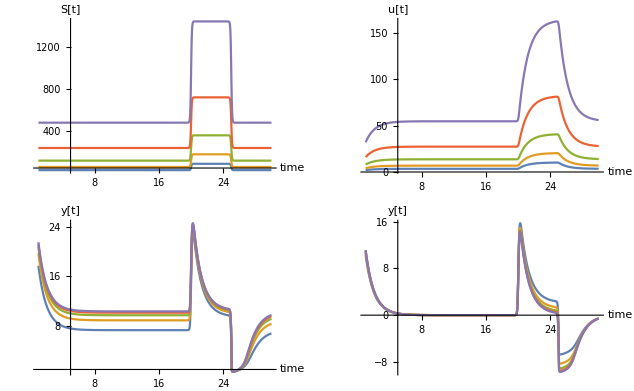

```mathematica
factors={1,2,4,8,16}30;
MyMax[f_,t0_,t1_]:=Max[f[t]/.t->Subdivide[t0,t1,300]]
GraphicsGrid[{{Plot[Evaluate[Table[Signal[t,S0,2S0,tStart,tDuration,tSharp]/.par,{S0,factors }]],{t,1,tMax/.par},PlotRange->{All,All},AxesLabel->{"time","S[t]"}],
Plot[Evaluate[Table[sol[S0,2 S0][[1]][t],{S0,factors }]],{t,1,tMax/.par},PlotRange->{All,All},AxesLabel->{"time","u[t]"}]},
{Plot[Evaluate[Table[sol[S0,2 S0][[2]][t],{S0,factors }]],{t,1,tMax/.par},PlotRange->{All,All},AxesLabel->{"time","y[t]"}],
Plot[Evaluate[Table[sol[S0,2 S0][[2]][t]-sol[S0,2 S0][[2]][15],{S0,factors }]],{t,1,tMax/.par},PlotRange->{All,All},AxesLabel->{"time","y[t]"}]}}]
```